# Analysing the atmospheric spectra of exoplanets

#### by Tomáš Pecher

Up until the early 1990s, the existence of exoplanets was largely speculative; while the concept of other planetary systems was considered possible, there was no direct evidence to confirm their existence. The first confirmed planets^[1] to be found beyond the Solar system were discovered in 1992 orbiting a pulsar in the Virgo constellation (these are, of course, uninhabitable due to the pulsar’s deadly radiation). Since then, a global effort of planet-hunting telescopes (most notably the Keplermission^[2]), have identified over 5000 exoplanets^[3]. Even more impressively, scientists have been able to assess the habitability of many exoplanets, using techniques like Eclipse Spectroscopy^[4] to infer the planets’ atmospheric composition. In this brief essay, I use the Wolfram language to replicate this atmospheric analysis on planets catalogued in the NASA exoplanetary archive^[5].

## Questions

The initial scope for this project was to answer the following:

What are the general trends/features of the atmospheric data?

Can we infer some basic information about atmospheric composition from the data?

Can we use machine learning to classify exoplanets based on their atmospheric data?

However, as I observed the spectra, I was surprised by just how detailed and informative the atmospheric data was. This lead me to consider assessing the planet’s habitability as a possibility and so I expanded the project’s scope to include the following:

Can we use statistical analysis to estimate the habitability of distant planets?

Of the tested exoplanets, which ones are most likely to be habitable?

A valid criticism of projects like these is the importance of answering such questions, after all we have far more pressing issues to deal with right here on Earth so why bother spending time and resources studying places that we may not be able to visit in a million years (or ever). While there is some credence to this, studying distant worlds is arguably the best way to learn about our own. Alongside theoretical ideas, such as the search for extraterrestrial life, exoplanetary atmospheric spectroscopy allows us to understand how our atmosphere came to be, how its components interact with one another and how they influence temperature, pressure and cosmic radiation. The state of the Earth’s atmosphere (with respect to these properties) is a fundamental reason why life has been allowed to exist on this planet, and as we continue to pollute it through unregulated emissions, only by understanding the inner workings of planetary atmospheres can we allow life to continue to exist as it is.

## Understanding the data

Before working with the extensive “full spectral data”, I decided to view the general experimental data provided on theexoplanet archive^[5]. This can be downloaded as a single CSV document which contains an overall description of each experiment, allowing us to learn about what types of data we are dealing with and plan out how we will process and explore it. There is a lot of redundant information that will have to be removed.

Set the current directory to that of the data folder to easily import data files:

```mathematica
SetDirectory[NotebookDirectory[] <> "planetaryData"]
```

/home/tom/Code/Git/Projects/Exoplanets/planetaryData

Import the general experiment dataset and view the first five entries:

```mathematica
atmosphericSpectroscopyData=Import["AtmosphericSpectroscopyData.csv","Dataset","HeaderLines"->1];
atmosphericSpectroscopyData[1;;5]
```

Select the relevant information and replace the current property names with more informative ones:

```mathematica
asDS=atmosphericSpectroscopyData[All,{"PL_NAME","SPEC_TYPE","NUM_DATAPOINTS","MINWAVELNG","MAXWAVELNG"}];
asDSnewkeys={
"PL_NAME"->"PLANET_NAME",                                               (* string *)
"SPEC_TYPE"->"SPECTRUM_TYPE",                                      (* string: emission/transmission *)
"NUM_DATAPOINTS"->"NUM_OF_DATAPOINTS",                  (* integer *)
"MINWAVELNG"->"MINIMUM_WAVELENGTH",                         (* microns *)
"MAXWAVELNG"->"MAXIMUM_WAVELENGTH"                            (* microns *)
};
asDS=asDS[All,KeyMap[#/. asDSnewkeys&,#]&];
asDS[1;;5]
```

Here we have the dataset of experiments. We can see which planets have been studied, how frequently, what type of spectroscopy was used (more on this later) and the range of the spectra. First, let’s see which exoplanets are included in the archive.

Show the names of all unique exoplanets:

```mathematica
DeleteDuplicates[Normal[asDS[All,"PLANET_NAME"]]]
```

{Kepler-6 b,Kepler-20 c,55 Cnc e,CoRoT-1 b,CoRoT-2 b,GJ 1214 b,GJ 436 b,HAT-P-12 b,HAT-P-13 b,HAT-P-14 b,HAT-P-16 b,HAT-P-18 b,HAT-P-19 b,HAT-P-1 b,HAT-P-23 b,HAT-P-26 b,HAT-P-2 b,HAT-P-30 b,HAT-P-32 b,HAT-P-33 b,HAT-P-3 b,HAT-P-4 b,HAT-P-6 b,HAT-P-8 b,HD 149026 b,HD 189733 b,HD 209458 b,HD 97658 b,Qatar-1 b,TrES-1 b,TrES-3 b,TrES-4 b,WASP-10 b,WASP-12 b,WASP-14 b,WASP-17 b,WASP-18 b,WASP-19 b,WASP-21 b,WASP-24 b,WASP-25 b,WASP-26 b,WASP-29 b,WASP-2 b,WASP-31 b,WASP-32 b,WASP-33 b,WASP-36 b,WASP-39 b,WASP-3 b,WASP-43 b,WASP-45 b,WASP-46 b,WASP-48 b,WASP-4 b,WASP-5 b,WASP-6 b,WASP-8 b,XO-1 b,XO-2 N b,XO-3 b,XO-4 b,WASP-78 b,WASP-79 b,KELT-1 b,KELT-2 A b,GJ 3470 b,HAT-P-40 b,HAT-P-41 b,WASP-49 b,WASP-62 b,WASP-63 b,WASP-67 b,WASP-57 b,WASP-52 b,WASP-77 A b,WASP-64 b,WASP-80 b,KELT-3 b,HATS-2 b,WASP-65 b,WASP-103 b,WASP-96 b,WASP-97 b,WASP-98 b,WASP-100 b,WASP-101 b,WASP-117 b,WASP-104 b,WASP-94 A b,WASP-69 b,K2-3 b,K2-3 c,K2-3 d,KELT-7 b,HAT-P-55 b,WASP-74 b,K2-18 b,HAT-P-57 b,GJ 1132 b,HAT-P-51 b,K2-26 b,WASP-76 b,TRAPPIST-1 b,TRAPPIST-1 c,WASP-124 b,WASP-121 b,HIP 41378 b,HIP 41378 f,HD 3167 c,HAT-P-65 b,WASP-131 b,WASP-127 b,TRAPPIST-1 g,TRAPPIST-1 h,HD 106315 c,LHS 1140 b,KELT-11 b,KELT-9 b,WASP-107 b,WASP-156 b,GJ 9827 d,KELT-20 b,LHS 1140 c,HD 219666 b,V1298 Tau b,WASP-87 b,TOI-270 c,TOI-270 d,LTT 1445 A b,HAT-P-70 b,WASP-178 b,V1298 Tau c,L 168-9 b,LTT 9779 b,GJ 486 b,TOI-674 b,GJ 367 b,TOI-1268 b,WASP-189 b,Kepler-18 c,Kepler-410 A b,LHS 475 b,Kepler-61 b,KOI-13 b,Kepler-102 e,Kepler-14 b,Kepler-94 b,Kepler-125 b,TOI-4438 b,TOI-4860 b,Kepler-68 b,Kepler-62 e,Kepler-249 d,KOI-94 d,Kepler-32 d,Kepler-49 c,Kepler-20 d,Kepler-26 c,Kepler-102 d,Kepler-11 e,Kepler-25 c,Kepler-37 d,Kepler-127 d,Kepler-25 b,Kepler-93 b,TrES-2 b,Kepler-18 d,Kepler-104 d,Kepler-126 d,Kepler-51 d,Kepler-138 c,Kepler-138 d,Kepler-22 b,Kepler-9 b,Kepler-5 b,Kepler-236 c,Kepler-10 c,Kepler-19 b,Kepler-49 b,HAT-P-7 b,KOI-12 b,K2-24 b,HAT-P-11 b,Kepler-9 c,Kepler-158 c,Kepler-205 c}

Using Wolfram’s “WordCloud[]” function, we can see which planets have been studied the most:

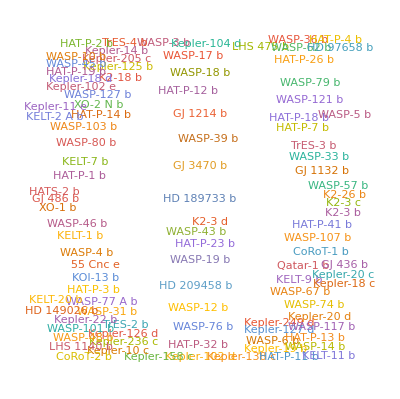

```mathematica
WordCloud[Counts[Normal[asDS[All,"PLANET_NAME"]]]]
```

Just from this basic word cloud we can see that some exoplanets get most of the attention (proportional to how “cool” they are, for instance HD 189733 b is well-known for its incredible windspeeds and for glass raining from its skies^[6]) whereas the majority are tested sparsely. However, to explore this idea further, we have to create an actual data plot.

By plotting how many experiments were conducted on each planet, we see that most planets are tested only a few times whereas some have 20+ experiments:

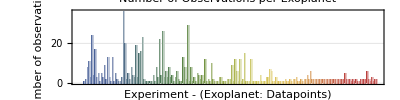

```mathematica
BarChart[(Tooltip[#[[2]],#[[1]]<>": "<>ToString[#[[2]]]]&)/@Tally[Normal[asDS[All,"PLANET_NAME"]]],
FrameLabel->{"Experiment - (Exoplanet: Datapoints)","Number of observations"},
PlotLabel->"Number of Observations per Exoplanet",
AspectRatio->0.25,
PlotTheme->"Detailed",
ChartStyle->"DarkRainbow",
ChartElementFunction->"FadingRectangle",
ImageSize->Full
]
```

This can be better visualised with a histogram:

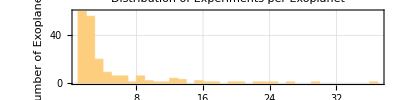

```mathematica
Histogram[Counts[Normal[asDS[All,"PLANET_NAME"]]],
FrameLabel->{"Number of Experiments","Number of Exoplanets"},
PlotLabel->"Distribution of Experiments per Exoplanet",
PlotRange->Full,
PlotTheme->"Detailed",
ImageSize->Full,
AspectRatio->0.25
]
```

Again, we see that the number of experiments per exoplanet follows (almost) a reciprocal distribution. Nevertheless, this general data tells us nothing about the spectrum tested for each planet. Let’s answer that now.

Plot the ranges of tested wavelengths in each experiment:

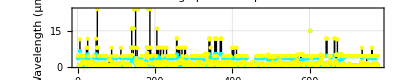

```mathematica
Show[{
	ListPlot[Table[Normal[asDS[[i,"MAXIMUM_WAVELENGTH"]]],{i,Length[asDS]}],PlotStyle->Red,PlotTheme->"Detailed"],
	ListPlot[Table[Normal[asDS[[i,"MINIMUM_WAVELENGTH"]]],{i,Length[asDS]}]],
		Graphics[Table[Line[{{i,Normal[asDS[[i,"MINIMUM_WAVELENGTH"]]]},{i,Normal[asDS[[i,"MAXIMUM_WAVELENGTH"]]]}}],{i,Length[asDS]}]],
		Graphics[Table[{PointSize[Small],Cyan,Point[{i,Normal[asDS[[i,"MINIMUM_WAVELENGTH"]]]}]},{i,Length[asDS]}]],
		Graphics[Table[{PointSize[Small],Yellow,Point[{i,Normal[asDS[[i,"MAXIMUM_WAVELENGTH"]]]}]},{i,Length[asDS]}]]
		},
	FrameLabel->{"Experiment Index","Wavelength (μm)"},
	PlotLabel->"Testing Spans of Experiments",
	PlotRange->Full,
	DataRange->Full,
    ImageSize->Full,
	AspectRatio->0.2
]
```

Notice that this (rather crude) graph has two bands centred around λ = 1.4μm and λ = 4.3μm. This is almost certainly because these are some of the key wavelengths of light that are absorbed by water and carbon dioxide respectively (however we cannot confirm this as some may have tested for other compounds which also absorb light in that range, such as silicon monoxide).

## Data wrangling

### Obtaining the data

Now let’s move on to the actual spectral data. Rather than providing a single CSV file containing data for each experiment (like the general data), you download each exoplanet’s experimental data separately using a wget script. The data for each planet comes in individual table (.tbl) files, which are essentially ASCII tables, and as far as I can tell are not supported in the Wolfram language. Therefore, to extract the data, I wrote a function that parses each file.

Parsing function removes ASCII grid and extracts the data:

```mathematica
extractTBL[filePath_]:=Module[{data,colNameRows,colNames,delimPos},
data=ReadList[filePath,String];
colNameRows=Flatten[Position[data,s_String/;StringTake[s,1]=="|"]];
colNames=StringTrim/@StringSplit[data[[colNameRows[[1]]]],"|"];
delimPos=Union[Flatten[StringPosition[data[[colNameRows[[1]]]],"|"]]];
data=Table[Map[StringTrim[StringTake[data[[i]],{#[[1]]+1,#[[2]]-1}]]&,Partition[delimPos,2,1]],{i,colNameRows[[-1]]+1,Length[data]}];
Association[MapThread[Rule,{colNames,Transpose[data]}]]]
```

Set the current directory to that of the spectrum data:

```mathematica
SetDirectory[NotebookDirectory[] <> "spectrumData"]
```

/home/tom/Code/Git/Projects/Exoplanets/spectrumData

Run the parsing function on all the .tbl files and store the data in a dataset:

```mathematica
tbls=Select[FileNames[],StringContainsQ[#,".tbl"]&];
fullSpectrumData=Dataset[Table[extractTBL[tbls[[i]]],{i,Length[tbls]}]];
```

Select the necessary information and display the first 5 entries:

```mathematica
fsDS=fullSpectrumData[All,{"CENTRALWAVELNG","ESPECLIPDEP","PL_TRANDEP"}];
fsDS[1;;5]
```

As we can see, the data we need for this analysis are the wavelengths being measured (independent variable) and the transit depth (the measured wavelength-dependent decrement in relative flux caused by the planet transiting in front of the star (NASA Exoplanet Archive User(Guide))^[7]. We must now clean the data.

For the sake of consistency, I rename the properties of this dataset appropriately:

```mathematica
fsDSnewkeys:={
"CENTRALWAVELNG"->"CENTRAL_WAVELENGTH",                 (* microns *)
"ESPECLIPDEP"->"ECLIPSE_DEPTH",                                    (* percentage *)
"PL_TRANDEP"->"TRANSIT_DEPTH"                                         (* percentage *)
}
fsDS=fsDS[All,KeyMap[#/. fsDSnewkeys&,#]&];
```

Next, we convert the string data into floating points (this will allow an easier conversion to Wolfram quantities later):

```mathematica
fsDS=Map[If[MissingQ[#],#,ToExpression[#]]&,fsDS,{2}];
fsDS[1;;5]
```

### Cleaning the data

While we now have our raw data in a dataset object, we must first refine the data before using it in plots or calculations. This includes removing missing entries, converting numerical values to their appropriate units and finally checking its validity.

Find the “names” of each experiment based on the file names:

```mathematica
expNames=StringReplace[#,{".tbl"->""}]&/@FileNames[];
```

Create a list of Boolean based on whether the dependent variable “eclipse depth (%)” is missing:

```mathematica
missing=Not/@MissingQ/@Normal[fsDS[All,"TRANSIT_DEPTH"]];
```

NOTE: The basic premise of ecliptic atmospheric spectroscopy involves observing the change in spectrum of light as the exoplanet eclipses its host star. NASA’s experimental data contains a mix of data from two types of spectroscopy (although the underlying principle remains the same). Transmission spectroscopy is conducted during the exoplanet’s first eclipse (when the exoplanet passes in-front of its star: a transit) whereas emission spectroscopy is conducted during the second eclipse (when the exoplanet passes behind its star). As a result, NASA’s archive puts the data for each type in separate columns, therefore and experiment either has eclipse depth data or transit depth data. By filtering all the experiments without transit depth data, I am left with data only from transmission spectroscopy experiments which I will be focussing on for this notebook. I have left the emission data in the old dataset for those who want to extend the methods in this notebook to this alternative data.

Remove missing data, leaving only transmission spectroscopy data:

```mathematica
cwl=Pick[Normal[fsDS[All,"CENTRAL_WAVELENGTH"]],missing];
tsd=Pick[Normal[fsDS[All,"TRANSIT_DEPTH"]],missing];
exps=Pick[expNames,missing];
```

Convert  the remaining data into its appropriate units:

```mathematica
cwlUnits=Map[Quantity[#,"Micrometers"]&,cwl,{2}];
tsdUnits=Map[Quantity[#,"Percent"]&,tsd,{2}];
```

```mathematica
tsDS=Dataset[Association/@Transpose[{
Rule["EXPERIMENT",#]&/@exps,
Rule["CENTRAL_WAVELENGTH",#]&/@cwlUnits,
Rule["TRANSIT_DEPTH",#]&/@tsdUnits
}]]
```

Dataset[<>]

As a sanity check, I plot the tested data points to see if they match up to the original plot of wavelength ranges from the general data (and indeed they do although there are now less data points since we removed the emission data).

Plot the experimental coverage of the final, cleaned data:

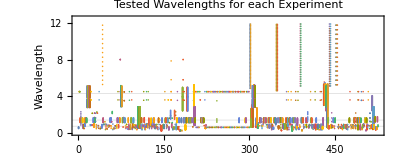

```mathematica
ListPlot[Table[Transpose[{
ConstantArray[i,Length[Normal[tsDS[All,"CENTRAL_WAVELENGTH"]][[i]]]],
Normal[tsDS[All,"CENTRAL_WAVELENGTH"]][[i]]
}],{i,Length[tsDS]}],
FrameLabel->{"Experiment","Wavelength"},
PlotLabel->"Tested Wavelengths for each Experiment",
PlotRange->{0,12.5},
DataRange->Full,
ImageSize->Full,
AspectRatio->0.4,
GridLines->{{},{0.73,1.4,4.3}}, (* strongest spectral features of Subscript[O, 2], Subscript[H, 2] O and Subscript[CO, 2] respectively *)
GridLinesStyle->Thin,
PlotTheme->"Detailed",
ImageSize->Full
]
```

## Data exploration

### Visualization

Now that we have a clean dataset, we are finally ready to visualize the data. We start off basic by plotting the spectra as they were intended.

Plot the transit depth against the wavelength of light being observed:

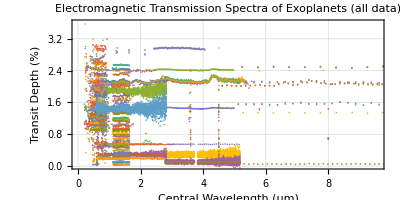

```mathematica
ListPlot[Thread/@Transpose[{Normal[tsDS[All,"CENTRAL_WAVELENGTH"]],Normal[tsDS[All,"TRANSIT_DEPTH"]]}],
FrameLabel->{"Central Wavelength (μm)","Transit Depth (%)"},
PlotLabel->"Electromagnetic Transmission Spectra of Exoplanets (all data)",
PlotRange->{0, 3.6},
DataRange->Full,
PlotTheme->"Detailed",
ImageSize->Full,
AspectRatio->0.5
]
```

We can see that the experiments can be described as belonging to one of three groups. Some of the experiments test only single values or a single wavelength multiple times, most likely to reproduce measurements from other experiments. Other experiments, especially those testing wavelengths below 2μm, systematically test over a narrow range of wavelengths as they look for the characteristic peak produced by the existence of certain compounds (such as water and oxygen). The last group of experiments have upwards of 100 data points each and test over a wide range of frequencies and hence generally testing to see what compounds exist rather than testing for a specific one. Many of the larger experiments also contain gaps in the spectra at exactly the same places, and I have been unable to find a good explanation as to why this is. If I were to assume, I would say that there are no significant peaks in those areas and so they removed them from testing to conserve resources.

Viewing the data on a log-linear plot allows us to see some of the finer details:

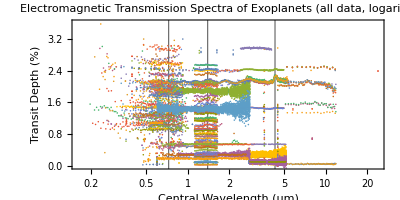

```mathematica
ListLogLinearPlot[Thread/@Transpose[{Normal[tsDS[All,"CENTRAL_WAVELENGTH"]],Normal[tsDS[All,"TRANSIT_DEPTH"]]}],
FrameLabel->{"Central Wavelength (μm)","Transit Depth (%)"},
PlotLabel->"Electromagnetic Transmission Spectra of Exoplanets (all data, logarithmic)",
PlotRange->{0, 3.6},
DataRange->Full,
PlotTheme->"Detailed",
ImageSize->Full,
GridLines->{{0.73,1.4,4.3},{}}, (* strongest spectral features of Subscript[O, 2], Subscript[H, 2] O and Subscript[CO, 2] respectively *)
GridLinesStyle->Directive[{ Thin,Black}],
AspectRatio->0.5
]
```

The long-band data is some of the most interesting as it shows multiple peaks.

Plot the experimental spectra with at least d data points:

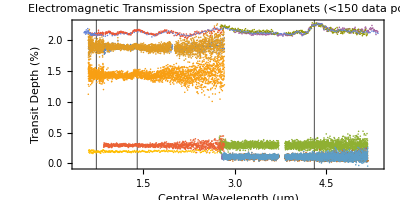

```mathematica
Module[{d,planets,centralwavelengths,transitdepths},
d=150;
planets=Pick[Normal[tsDS[All,"EXPERIMENT"]],Length[#]>=d&/@Normal[tsDS[All,"TRANSIT_DEPTH"]]];
centralwavelengths=Pick[Normal[tsDS[All,"CENTRAL_WAVELENGTH"]],Length[#]>=d&/@Normal[tsDS[All,"TRANSIT_DEPTH"]]];
transitdepths=Pick[Normal[tsDS[All,"TRANSIT_DEPTH"]],Length[#]>=d&/@Normal[tsDS[All,"TRANSIT_DEPTH"]]];
ListPlot[Table[Tooltip[Transpose[{centralwavelengths[[i]],transitdepths[[i]]}],planets[[i]]],{i,Length[planets]}],
FrameLabel->{"Central Wavelength (μm)","Transit Depth (%)"},
PlotLabel->"Electromagnetic Transmission Spectra of Exoplanets (<150 data points)",
PlotRange->Full,
DataRange->Full,
ImageSize->Full,
PlotTheme->"Detailed",
GridLines->{{0.73,1.4,4.3},{}}, (* strongest spectral features of Subscript[O, 2], Subscript[H, 2] O and Subscript[CO, 2] respectively *)
GridLinesStyle->Directive[{ Thin,Black}],
AspectRatio->0.5
]]
```

With this “Manipulate[]” we can dynamically view each spectrum as we wish:

```mathematica
With[{
centralwavelengths=Thread/@Transpose[{Normal[tsDS[All,"CENTRAL_WAVELENGTH"]],Normal[tsDS[All,"TRANSIT_DEPTH"]]}]
},
Manipulate[
ListLinePlot[centralwavelengths[[exp]],
FrameLabel->{"Central Wavelength (μm)","Transit Depth (%)"},
PlotLabel->"Transmission Spectrum: "<>Normal[tsDS[All,"EXPERIMENT"]][[exp]],
ImageSize->Large,
PlotTheme->"Detailed",
PlotRange->Full,
GridLines->{{0.73,1.4,4.3},{}}, (* strongest spectral features of Subscript[O, 2], Subscript[H, 2] O and Subscript[CO, 2] respectively *)
AspectRatio->0.5,
PlotStyle->Black,
Mesh->Full,
MeshStyle->Hue[exp/Length[tsDS]]
],{{exp,429},1,Length[tsDS],1}
]]
```

### Summary Statistics

Let’s also generate summary statistics for each set of data.

Number of data points, mean, standard deviation and skew:

```mathematica
n=Length/@Normal[tsDS[All,"TRANSIT_DEPTH"]];
μ=Mean/@Normal[tsDS[All,"TRANSIT_DEPTH"]];
σ=If[Length[#]==1,Missing,StandardDeviation[#]]&/@Normal[tsDS[All,"TRANSIT_DEPTH"]]/.Sqrt["Percent"^2]->"%";
skew=If[Length[#]==1,Missing,Skewness[#]]&/@Normal[tsDS[All,"TRANSIT_DEPTH"]];
(* Standard deviation and skew both require at least 2 unique data points. *)
```

Tukey’s five number summary (minimum, lower quartile, median, upper quartile, maximum):

```mathematica
tdmin=Min/@Normal[tsDS[All,"TRANSIT_DEPTH"]];
tdmax=Max/@Normal[tsDS[All,"TRANSIT_DEPTH"]];
{tdlq,tdmed,tduq}=Transpose[Quartiles/@Normal[tsDS[All,"TRANSIT_DEPTH"]]];
```

Store the summary statistics in a dataset:

```mathematica
ssDS=Dataset[Association/@Transpose[{
Rule["EXPERIMENT",#]&/@exps,
Rule["n",#]&/@n,
Rule["μ",#]&/@μ,
Rule["σ",#]&/@σ,
Rule["skew",#]&/@skew,
Rule["tdmin",#]&/@tdmin,
Rule["tdlq",#]&/@tdlq,
Rule["tdmed",#]&/@tdmed,
Rule["tduq",#]&/@tduq,
Rule["tdmax",#]&/@tdmax,
Rule["iqr",#]&/@(tduq-tdlq)
}]]
```

Dataset[<>]

Create box-whisker chart base on these statistics:

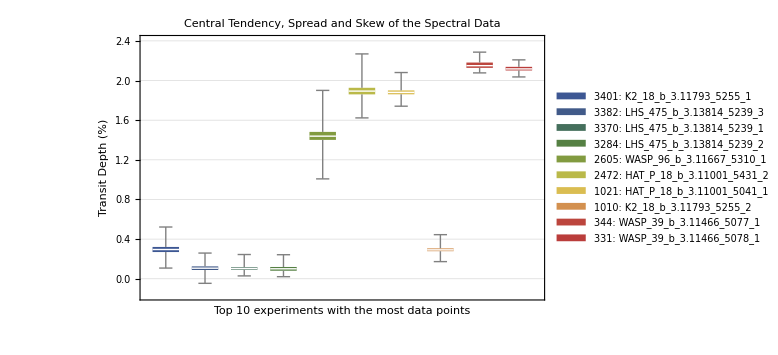

```mathematica
With[{
legend=MapThread[#1<>": "<>#2&,
{ToString/@Normal[TakeLargest[ssDS[All,"n"],10]],
Normal[ssDS[Flatten[Position[ssDS[All,"n"],#]&/@TakeLargest[Normal[ssDS[All,"n"]],10]],"EXPERIMENT"]]}
]},
Show[
BoxWhiskerChart[Take[ReverseSortBy[Normal[tsDS[All,"TRANSIT_DEPTH"]],Length],10],
PlotRange->Full,
ImageSize->Large,
ChartStyle->"DarkRainbow",
ChartLegends->legend,
PlotTheme->"Detailed"
],
FrameLabel->{{"Transit Depth (%)",None},{"Top 10 experiments with the most data points",None}},
PlotLabel->"Central Tendency, Spread and Skew of the Spectral Data"
]]
```

Due to the density of the data, I found the distribution chart to be more informative:

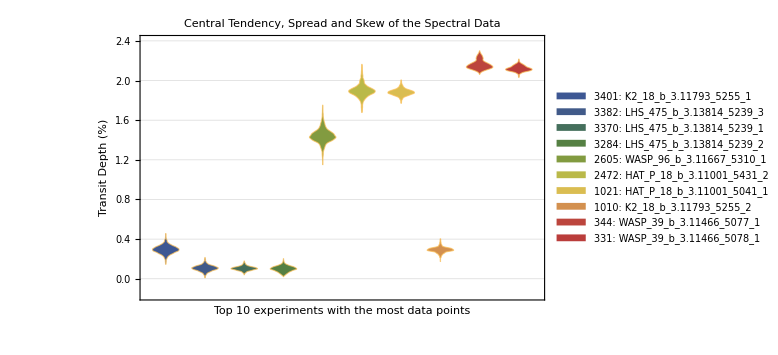

```mathematica
With[{
legend=MapThread[#1<>": "<>#2&,
{ToString/@Normal[TakeLargest[ssDS[All,"n"],10]],
Normal[ssDS[Flatten[Position[ssDS[All,"n"],#]&/@TakeLargest[Normal[ssDS[All,"n"]],10]],"EXPERIMENT"]]}
]},
Show[
DistributionChart[Take[ReverseSortBy[Normal[tsDS[All,"TRANSIT_DEPTH"]],Length],10],
PlotRange->Full,
ImageSize->Large,
ChartStyle->"DarkRainbow",
ChartLegends->legend,
PlotTheme->"Detailed"
],
FrameLabel->{{"Transit Depth (%)",None},{"Top 10 experiments with the most data points",None}},
PlotLabel->"Central Tendency, Spread and Skew of the Spectral Data"
]]
```

### Exploration Conclusions

From visualizing the data, we were able to learn a number of key things. First, that there are 3 groups of experiment conducted in the dataset: single value tests done to verify individual measurements, narrow-band tests which look to confirm the presence of specific compounds and wide-band tests which arbitrarily test for multiple compounds in the atmospheric composition. From the scatter plots, we can also observe significant peaks in the spectra which correspond to key absorption wavelengths of life-giving compounds (such as water, oxygen and carbon dioxide, which my imply the presence of life). The magnitude of these peaks demonstrate that using the appropriate mathematical methods, it would be possible to infer the presence of such chemicals from the spectra to an adequate level of accuracy.

By labelling each dataset with its associated planet and using dynamic plots, we were able to see which exoplanets where tested and which one of the three testing frameworks was performed. From this, we saw (especially with the experiments of <100 data points) that some planets were tested multiple times, and crucially, that repeated experiments on the same planets yielded almost identical results (as seen by the spectra completely overlapping). This consistency tells us that we could, in theory, learn to recognize planets based on their atmospheric "fingerprint", which is what inspired my to apply machine learning to this project. An important consideration when deploying machine learning is whether your data has an learnable underlying pattern and is not just completely random (we could train a model to classify random noise to 100% certainty yet achieve 0% accuracy on new data simply due to randomness). The confirmation that the experiments are significant in this regard.

Equally interesting to this was the summary statistics. At a glance, we see that for the vast majority of the experiments, the data was highly concentrated around the central transit depth, demonstrated by the unusually measures of spread (standard deviations and interquartile ranges). The same cannot be said for the ranges of the data which are abnormally wide in proportion to the quartiles; it seems that while the data is not extremely noisy, what noise does exist manifests as quite extreme values. It soon became very obvious that little information about the peaks of the spectra could be obtained from the summary statistics as most experiments showed almost perfectly symmetrical data distributions (this can be observed visually from the distribution charts but also from the summary data: the median values are very close to the mean values and the skews are unusually low). A faint bimodal distribution can be observed in the 9^th example in the distribution chart which suggests that said spectrum contains peaks but this is a rare case where the data range is less extreme.

From the visualizations of the data and the summary statistics, we can conclude two things. First, that there is real, useful information about the exoplanets' atmospheres encoded withing the spectra provided, and so the use of ML and spectral analysis techniques are justified. However, second, that the data is noisy, and specifically that the fluctuations of the noise are similar in magnitude to the spectral peaks that are caused by the presence of atmospheric compounds. Therefore, if spectral analysis is to be used to make judgements about the habitability of these exoplanets, precautions must be taken to reduce the noise in the data without unintentionally removing the true absorption peaks.

## Data analysis

### Analysis 1: Exoplanet classifier using ML

In this first analysis, I attempt to find out just how informative the spectral data of each exoplanet really is. If there is truly some knowledge about an exoplanet’s atmosphere encoded within its spectrum (as well as other factors such as the size of the planet and luminosity of its host star), it should be possible to use this spectrum as an “atmospheric fingerprint” for that exoplanet. Hence, once could then train an ML classifier to identify exoplanets based on this fingerprint.

This analysis serves as a proof of concept, so while it is in theory possible to include all of the exoplanets in the classification, (for training time reasons) I chose only to classify the exoplanets with the most data, specifically those with at least 150 data points (resulting in 6 exoplanets and so 6 classes):

Obtain data from dataset:

```mathematica
With[{cutoff=150},
exoplanets=Pick[StringDrop[StringSplit[#,"."][[1]],-2]&/@Normal[tsDS[All,"EXPERIMENT"]],Length[#]>=cutoff&/@Normal[tsDS[All,"TRANSIT_DEPTH"]]];
transitData=Pick[Thread/@Transpose[{Normal[tsDS[All,"CENTRAL_WAVELENGTH"]],Normal[tsDS[All,"TRANSIT_DEPTH"]]}],Length[#]>=cutoff&/@Normal[tsDS[All,"TRANSIT_DEPTH"]]]];
```

Number of classes:

```mathematica
Length[DeleteDuplicates[exoplanets]]
```

6

To avoid introducing bias into the training data, the full dataset was rearranged randomly. Given the decent size of the dataset, I opted for a 70-30 train-test split. Since this is just a single proof of concept,  there is no need for a validation dataset, however if I were to extend this analysis (perhaps by observing the decrease in model accuracy as more classes are added), I would instead split the data by 65-25-10.

Reformat data into a single randomized list of input/output pairs:

```mathematica
classifierData=RandomSample[Flatten[Table[Rule[#,exoplanets[[i]]]&/@transitData[[i]],{i,Length[exoplanets]}]]];
Length[classifierData]
```

21897

Split the data into a training and test dataset:

```mathematica
With[{partition=Round[0.7*Length[classifierData]]},
trainingData=classifierData[[;;partition]];
testingData=classifierData[[partition;;]]];
{Length[trainingData],Length[testingData]}
```

{15328,6570}

Now we can train the model. For this dataset, Wolfram’s “Classify” superfunction uses a variety of algorithms but in my version (13.1) most often employs gradient-boosted trees which is promising as it is a sensible choice.

Train the classifier:

```mathematica
model=Classify[trainingData]
```

Once training is complete, we can run the model on the test dataset and count up how many data points were successfully mapped to their corresponding exoplanet. From this, we can calculate the models accuracy which, from my experimentation, almost always sits between 98-99% accuracy, a pretty satisfying result.

Run the classifier on the test data and count the number of correct classifications:

```mathematica
correct=Count[Equal[#[[1]],#[[2]]]&/@Transpose[{model[Keys[testingData]],Values[testingData]}],True]
```

6494

Compute the accuracy:

```mathematica
accuracy=N[correct/Length[testingData],5]
```

0.98843

However, those familiar with ML will know that we cannot assess the model’s performance based on accuracy alone. Using “ClassifierMeasurements” we can calculate the precision and recall for each class. The precision of a class is the proportion of all data points classified by the model to be in said class that are actually members of that class. Conversely, the recall of a class if the proportion of all data points in said class and correctly classified as being in that class. Unlike the highly general measure of accuracy, we can observe the table below to see that the model struggles to identify some exoplanets more than others, as well as how exactly this failure occurs (lower precision for a particular exoplanet suggests that the model mistakes another similar exoplanet for this one, in addition, lower recall for a particular exoplanet suggests the model mistakes this exoplanet for another similar one). These measurements are especially useful since the classes are not of uniform size.

Compute performance metrics:

```mathematica
performanceMetrics=ClassifierMeasurements[model,testingData];
Transpose[Dataset[AssociationMap[performanceMetrics,{"Precision","Recall"}]]]
```

This data can be better visualized with a confusion matrix. While the model statistics are different each time one runs the model, I can point out some general trends that I have observed. Due to the high accuracy, we see that most data points are on the main diagonal. The most common cases of data points being misclassified is with HAT-P-18 b and the two WASP exoplanets, as well as K2-18 b, LHS-475 b and LTT-9779 b which the model commonly occasionally to distinguish between. If you refer back to the scatter plot of the <150 data point experiments, you will notice that these planets form two groups, one on top of the other. I hypothesize that whatever misclassification exists is caused at the edges of the spectra where the data points overlap which causes the model to mistake one exoplanet from another. This would explain the exact confusion result that we observe.

Compute confusion matrix:

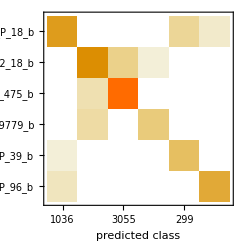

```mathematica
performanceMetrics["ConfusionMatrixPlot"]
```

### Analysis 2: Estimating habitability

As demonstrated by the model, not only is there information encoded in the exoplanetary spectra, but this information can be used to identify the specific planet to which it belongs. With this knowledge, I hope to do one final analysis to determine if we can use the spectral analysis techniques to extract information about the exoplanets’ atmospheric compositions from their spectra, and from this, make predictions about the habitability of said exoplanets.

While we all have a general sense of what it means for a place to be “habitable”, it is uniquely difficult to define mathematically as there are far too many factors that play into it. Moreover, whatever definition we give the term will almost certainly be wrong in the grander scale of the universe; who is to say that all life in the universe requires the same conditions as those on Earth.  As a result, we have to make a whole number of assumptions somewhere along the way. Therefore, for this project, we define the habitability of an exoplanet based on the likelihood that there is water present in the exoplanet’s atmosphere. However, I greatly encourage others to apply the same method to search for other compounds such as oxygen or carbon dioxide, or perhaps consider other data entirely such as estimated surface temperature to make a more rounded assessment of habitability.

First we need to gather the experiments that test within the main absorption peak of water.

Select experiments that test in the water range (at least 10 data points around 1.4μm):

```mathematica
waterData=QuantityMagnitude[Thread/@Transpose[{Normal[tsDS[All,"CENTRAL_WAVELENGTH"]],Normal[tsDS[All,"TRANSIT_DEPTH"]]}]];
validExps=Pick[exps,Table[Count[1.2<=#<=1.6&/@waterData[[i,All,1]],True]>=10,{i,Length[tsDS]}]];
waterData=Pick[waterData,Table[Count[1.2<=#<=1.6&/@waterData[[i,All,1]],True]>=10,{i,Length[tsDS]}]];
```

Plot the data:

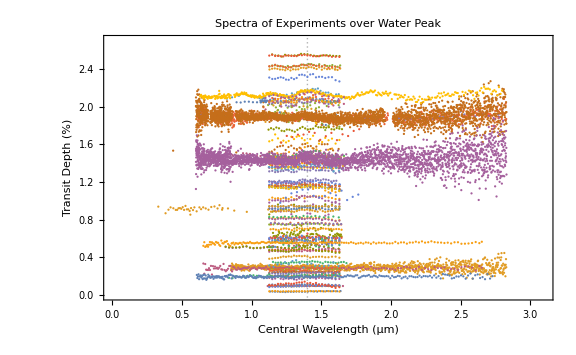

```mathematica
ListPlot[waterData,
ImageSize->Large,
GridLines->{{1.4},{}},
PlotRange->{{0,3.1},{0,2.7}},
PlotTheme->"Detailed",
FrameLabel->{"Central Wavelength (μm)","Transit Depth (%)"},
PlotLabel->"Spectra of Experiments over Water Peak"
]
```

We can see from the above graph that, while most experiments appear to have no peak around 1.4μm, some certainly do (this is most easily observed in the the spectra with the most data points). However, this is only visible because we are looking from 0-3μm so the data points are closer together, resulting in what appear to be more pronounced peaks. Zooming in to the neighbourhood of 1.4μm on the plot below, we see that any peaks are barely visible. This together with the noisiness of some of the experiments means that we cannot simply interpolate the value at 1.4μm and see how far above the mean it is. Instead, we will have to integrate over this interval and subtract the mean value.

Zoom in on the water range:

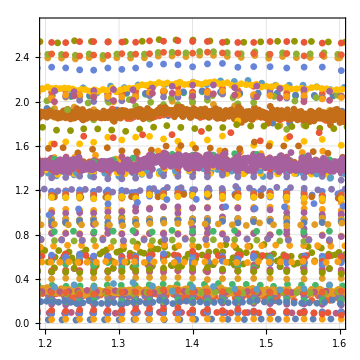

```mathematica
ListPlot[waterData,
PlotRange->{{1.2,1.6},{0,2.7}},
PlotMarkers->{"●",Tiny},
AspectRatio->1,
ImageSize->Medium,
PlotTheme->"Detailed"
]
```

In order to interpolate a set of data, each data point must have a unique x-value.Some experiments test the same value multiple times and for the sake of convenience, we will simply remove these.

Disregard experiments whose spectra cannot be interpolated (one-to-many values):

```mathematica
invalid=Position[Table[#==Union[#]&[Transpose[waterData[[i]]][[1]]],{i,Length[waterData]}],False];
waterData=Delete[waterData,invalid];
validExps=Delete[validExps,invalid];
```

Test if all remaining experiments are valid:

```mathematica
Union[Table[#==Union[#]&[Transpose[waterData[[i]]][[1]]],{i,Length[waterData]}]]
```

{True}

Before analyzing the whole dataset, let us take a look at the method used on a single example. Here is a spectrum with a relatively strong peak at 1.4μm.

Example spectrum relative to mean value:

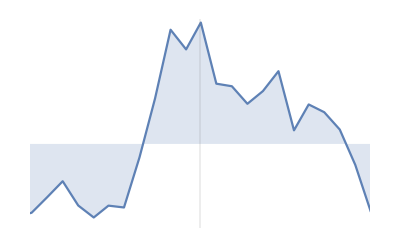

```mathematica
example=waterData[[34]];
ListLinePlot[example,
Axes->False,
AxesOrigin->{0,Mean[Transpose[example][[2]]]},
PlotRange->{{1.2,1.6},All},
Filling->Axis,
FillingStyle->Automatic,
GridLines->{{1.4},{}}
]
```

For the most accurate representation of an exoplanet’s atmospheric properties, we must first attempt to remove the unwanted fluctuations of the noise. To do this, we apply a Gaussian filter to the spectrum, thereby smoothing it and leaving only the general shape.

Applying a Gaussian filter to the spectrum:

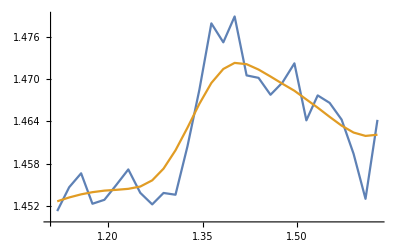

```mathematica
ListLinePlot[{example, Transpose[{Transpose[example][[1]], GaussianFilter[Transpose[example][[2]], 5]}]}]
```

Although the result already looks like some form of piecewise curve, this is simply a ListLinePlot and so the data is still only a list of values. In order to compute an integral, we must first fit a curve through this data. This is done below using a cubic interpolation.

Compute a cubic interpolation of the smoothed spectrum:

InterpolatingFunction[…]

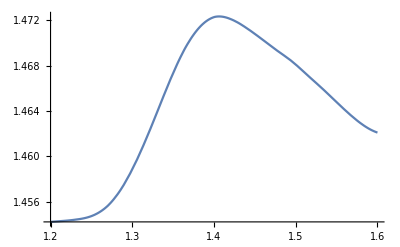

```mathematica
exampleInterpol=Interpolation[Transpose[{Transpose[example][[1]],GaussianFilter[Transpose[example][[2]],5]}]]
Plot[exampleInterpol[x],{x,1.2,1.6},PlotRange->All]
```

The method we will use for estimating the habitability of an exoplanet is as follows. For each interpolation, we will calculate the mean value of the curve. We can then integrate the difference between the curve and the mean value which will give us a measure of how much the original spectrum fluctuates and in what general direction (up or down). However, this measure considers the whole curve so we need a way of focussing specifically on the fluctuation around 1.4μm. This is achieved by multiplying the difference between curve and mean value by a “weight function” and then integrating to get the final score. I outline this approach in the cells below using a Normal distribution of μ=1.4 and σ=0.03.

Calculate the mean value of the curve:

```mathematica
meanValue=NIntegrate[exampleInterpol[x],{x,1.2,1.6}]/0.4
```

1.46438

Plot weight function:

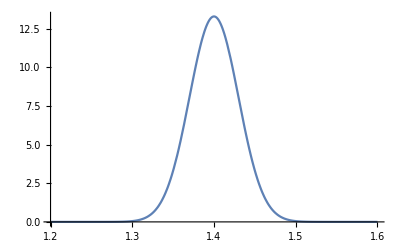

```mathematica
weightFunc[x_]:=PDF[NormalDistribution[1.4,0.03],x];
Plot[weightFunc[x],{x,1.2,1.6}]
```

Compute the integral:

```mathematica
NIntegrate[(exampleInterpol[x]-meanValue)weightFunc[x],{x,1.2,1.6}]
```

0.00671593

Here we arrive at our final score for this exoplanet’s spectrum. Admittedly, iIt on its own is not very informative, however we will see later this score is more telling (consistent with what we can observe from the spectra as humans) then what one may initially expect, especially when the scores of several exoplanets are compared together. Note how this method could be easily repurposed to search for the presence of any compound, simply by changing the primary absorption wavelength and the interval over which one integrates over. Future extensions of this project will almost certainly include calculating this score for several compounds and combining these along with temperature data or other factors: the possibilities are endless.

We are now ready to apply this method to the whole dataset.

Bundle the full method into a single module:

```mathematica
assessDataRange[data_]:=Module[{smooth,inpol,mean,diff},
(*smooth the data using Gaussian filter*)
smooth=Transpose[{#[[1]],GaussianFilter[#[[2]],5]}]&[Transpose[data]];
(*interpolate the smoothed data*)
inpol=Interpolation[smooth];
(*compute mean value over the range*)
mean=NIntegrate[inpol[x],{x,1.2,1.6}]/(1.6-1.2);
(*integrate weighted difference from the mean*)
diff=NIntegrate[(inpol[x]-mean)weightFunc[x],{x,1.2,1.6}];
(*return the metrics*)
{mean,inpol,diff}
]
```

The sizes of the absorption peaks that are observed in our spectra, while informative, are affected by a number of external factors (such as the size of the planet or the luminosity of its host star). For the purposes of this analysis, we are only concerned with whether a peak exists or not so to make the score fair, we must normalize the data so that it is within the same range for each experiment.

Normalize the spectra:

```mathematica
waterData=Table[Transpose[{#[[1]],Rescale[#[[2]]]}]&[Transpose[waterData[[i]]]],{i,Length[waterData]}];
```

Perform the computations and plot the results:

```mathematica
habitabilityresults=Module[{mean,inpol,diff},
Quiet[Sort[Table[{mean,inpol,diff}=assessDataRange[waterData[[i]]];
{i,
validExps[[i]],
ListLinePlot[waterData[[i]],
Axes->False,
AxesOrigin->{0,mean},
PlotRange->{{1.2,1.6},All},
Filling->Axis,
PlotStyle->Thin,
GridLines->{{1.4},{}}
],
Plot[inpol[x],{x,1.2,1.6},
Axes->False,
AxesOrigin->{0,mean},
PlotRange->{{1.2,1.6},All},
Filling->Axis,
GridLines->{{1.4},{}},
PlotStyle->Thin
],
diff
},
{i,Length[waterData]}],
#1[[-1]]>#2[[-1]]&]]];
```

NOTE: Some of the spectra do not have data points across the whole 1.2-1.6μm range. The Interpolation function, therefore, gives a warning each time it has to extrapolate outside of the actual range of the data it has been provided with. As a result, I have Quiet-ed this computation. This is not at detriment to the accuracy of the computation as all of the experiments have data near 1.4μm, and at the points where extrapolation does occur (further from 1.4μm), the weight function is near 0 so the effect is negligible.

Wrangle the data into a dataset object:

```mathematica
hDS=Dataset[Association/@Transpose[{
Rule["INDEX",#]&/@habitabilityresults[[All,1]],
Rule["EXPERIMENT",#]&/@habitabilityresults[[All,2]],
Rule["RAW_DATA",#]&/@habitabilityresults[[All,3]],
Rule["INTERPOLATION",#]&/@habitabilityresults[[All,4]],
Rule["WATER_SCORE",#]&/@habitabilityresults[[All,5]]
}]];
```

Finally, we arrive at the results. From the plots, we see that the interpolation step shows that the spectra are smoothed properly. The water score for each exoplanet is also consistent with the shape of each spectrum. From these top 10 results, we see that all the spectra show very strong peaks at 1.4μm which gradually get weaker as we go down the list. We see that the method works exactly as intended even in fringe cases such as experiment 33 which shows two peaks and a dip around 1.4μm. Given the size of the peaks either side 1.4μm, it is most likely that the dip was caused by noise in the measurements and we see that this method is not affected by this discrepancy, demonstrating its resilience compared to simple take the value of the interpolation at 1.4μm and subtracting the mean.

Show the top 10 experiments that most likely observed the presence of water in the exoplanet’s atmosphere:

```mathematica
hDS[[1;;10]]
```

The opposite end of the dataset further proves the validity of this method, as the spectra all show now absorption peak at 1.4μm.

Show the 5 least promising experiments:

```mathematica
hDS[[-5;;-1]]
```

However, this data only tells us about individual experiments. To successfully conclude this analysis, and indeed this project, we must gather the data for each exoplanet and use this to inform our final verdict about the most habitable planets in the exoplanetary archive.

Gather the experimental data by planet:

```mathematica
gatheredresults=GatherBy[Transpose[{StringDrop[StringSplit[#,"."][[1]]&/@Normal[hDS[[All,"EXPERIMENT"]]],-2],Normal[hDS[[All,"WATER_SCORE"]]]}],First];
```

Create a final dataset showing the habitability scores for each exoplanet:

```mathematica
finalDS=Dataset[Association/@ReverseSortBy[Transpose[{
Rule["PLANET_NAME",#]&/@gatheredresults[[All,1,1]],
Rule["EXPS",#]&/@Length/@gatheredresults[[All,All,-1]],
Rule["WATER_SCORES",#]&/@gatheredresults[[All,All,-1]],
Rule["CUMULATIVE_SCORE",#]&/@Total/@gatheredresults[[All,All,-1]],
Rule["MEAN_WATER_SCORE",#]&/@Mean/@gatheredresults[[All,All,-1]]
}],#[[-1]]&]]
```

As you can see,  I have listed the individual experimental scores for each exoplanet in the WATER_SCORES column. Most planets only have one experiment but some have more. Most would agree that if multiple separate experiments imply the presence of water in an exoplanets atmosphere, then this serves as more evidence that the exoplanet is habitable. As a result, I have computed two other metrics that take this into account. The CUMULATIVE_SCORE is the result of adding all of the water scores together, whereas the MEAN_WATER_SCORE is the mean of the water scores. The highest cumulative score goes to HD-209458 b and the highest mean score goes to V1298-Tauri b.

While the mean score is the best final measure of comparing habitability (and is what I use to sort the dataset), it does not come without its drawbacks. While a high mean score is good evidence for water to be present in the atmosphere, a single exceptional score can disproportionately place the planet’s habitability higher than it should be. For example, the best result (V1298-Tauri b) is impressive, however it could have just been an anomaly: in terms of evidence of water, it is therefore better to have multiple good scores then one exceptional score. For this reason, I included the cumulative score, which may have seemed strange however it takes this idea of mounting evidence into account, even if comparing values for this score may be unjustified as it is not an apples-to-apples comparison. Therefore, from the evidence provided in the exoplanetary archive, I predicted that HD-209458 b is the exoplanet most likely to be habitable.

### Verifying the results

To see if this prediction corroborated actual scientific research, I searched for HD-209458 b on NASA’s exoplanetcatalogue^[8] . I was pleased to read not only that  HD-209458 b has water vapour in its atmosphere, but that it was one of the first exoplanets^[9] discovered to have water (and one of the strongest absorption peaks, likely why it is the only exoplanet in this dataset with 4 experiments). This makes the atmospheric spectral analysis within this project an overwhelming success as these results directly corroborate those of proper scientific research. HD-209458 b’s habitability is a different story however; it is a gas giant slightly larger than Jupiter with an orbital radius 1/8 that of Mercury, which is almost as uninhabitable as it gets. As a result, I learnt that any metrics for habitability should include atmospheric composition as well as (at the very least) the orbital radius.

## Conclusions

Looking back at the objectives set out at the start of this project, it is amazing to see just how far it has come. As someone who is no expert in astrophysics, being able to explore the data for myself and learn about this field is fascinating. When I had started, I did not even know what an atmospheric spectrum might look like or how it is measured. In this project, we have observed the atmospheric spectra, pondered the 3 “types” of experiments that astronomers do, looked at the various fluctuations in the data and how they correspond to atmospheric compounds. We successfully applied machine learning to identify exoplanets based on their “atmospheric fingerprint”. Most impressively however, we were able to successfully extract quantitative data about the exoplanets’ atmospheres from their spectra and we were even able to make predictions about the habitability of exoplanets.

In the future, I hope to extend this project by building on the spectral analysis and how that relates to habitability. I will reuse the same method to search for multiple different compounds that are associated with life and habitable environments. In addition, I will factor in more data about each exoplanet outside of its atmospheric spectrum, such as orbital radius, stellar luminosity and estimating surface temperature.

## References

Historic timeline (2022) NASA. Available at: https://exoplanets.nasa.gov/alien-worlds/historic-timeline/#first-exoplanets-discovered (Accessed: 15 August 2024).

Kepler / K2 (2024) NASA. Available at: https://science.nasa.gov/mission/kepler/ (Accessed: 15 August 2024).

How many exoplanets are there? (2024) NASA. Available at: https://science.nasa.gov/exoplanets/how-many-exoplanets-are-there/ (Accessed: 15 August 2024).

Eclipse spectroscopy (2023) ESA. Available at: https://www.esa.int/ESA_Multimedia/Images/2023/09/Eclipse_spectroscopy (Accessed: 15 August 2024).

NASA Exoplanet Archive (2024) Caltech. Available at: https://exoplanetarchive.ipac.caltech.edu/docs/data.html (Accessed: 15 August 2024).

Rains of terror on Exoplanet HD 189733b (2016) NASA. Available at: https://www.nasa.gov/image-article/rains-of-terror-exoplanet-hd-189733b/ (Accessed: 03 September 2024).

Atmospheric Spectroscopy Data User Guide (2024) NASA. Available at: https://exoplanetarchive.ipac.caltech.edu/cgi-bin/atmospheres/nph-firefly?atmospheres (Accessed: 15 August 2024).

HD 209458 B - NASA Science (2024) NASA. Available at: https://science.nasa.gov/exoplanet-catalog/hd-209458-b/ (Accessed: 06 September 2024).

Hubble traces subtle signals of water on Hazy Worlds - NASA Science (2013) NASA. Available at: https://science.nasa.gov/missions/hubble/hubble-traces-subtle-signals-of-water-on-hazy-worlds (Accessed: 06 September 2024).